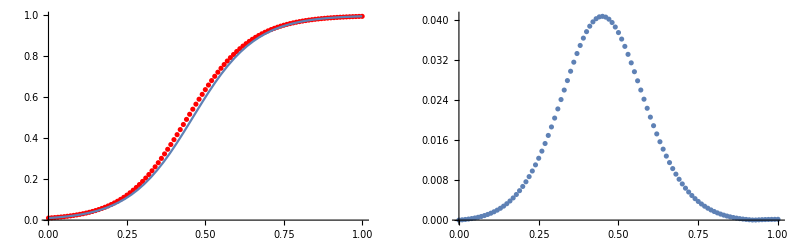

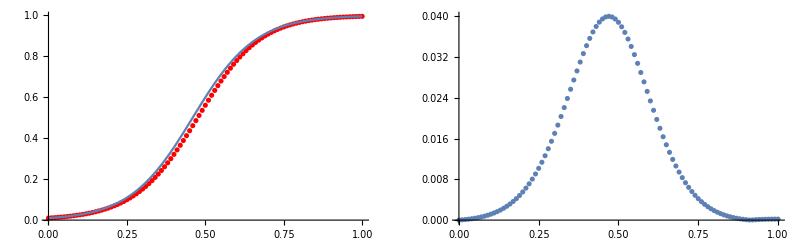

```mathematica
f[y_]:=10*y*(1-y);

logisticIC = 0.01;
logisticExact[t_]:=0.01/(0.01+0.99E^(-10t))

implicitEuiler[f_,y0_,n_,T_] := (
Block[{h,y,x,i,explicitStep},
h = N[T/n];
y=Table[0,{i,0,n}];
y[[1]]= y0;
For[i=1,i<=n,++i,
explicitStep=y[[i]]+10*h*y[[i]]*(1-y[[i]]);
y[[i+1]]= yNext /. FindRoot[y[[i]]+10*h*yNext(1-yNext)==yNext,{yNext,explicitStep}];
];
Table[{h*(i-1),y[[i]]},{i,1,Length[y]}]
]
);

explicitEuiler[f_,y0_,n_,T_] := (
Block[{h,y,x,i,explicitStep},
h = N[T/n];
y=Table[0,{i,0,n}];
y[[1]]= y0;
	For[i=1,i≤n,++i,
	y[[i+1]]=y[[i]]+h*10y[[i]]*(1-y[[i]]);
	];
	Table[{h*(i-1),y[[i]]},{i,1,Length[y]}]
]
);


solImplicit=implicitEuiler[f,0.01,100,1];

errorImlicit = Table[{solImplicit[[i,1]],Abs[logisticExact[solImplicit[[i,1]]]-solImplicit[[i,2]]]},{i,1,Length[solImplicit]}];

solExplicit = explicitEuiler[f,logisticIC,100,1];

errorExplicit= Table[{solExplicit[[i,1]],Abs[logisticExact[solExplicit[[i,1]]]-solExplicit[[i,2]]]},{i,1,Length[solExplicit]}];


GraphicsRow[
{Show[{
ListPlot[solImplicit,PlotStyle->Red],
Plot[logisticExact[t1],{t1,0,1}]
}],
ListPlot[errorImlicit]
}]
GraphicsRow[
{Show[{
ListPlot[solExplicit,PlotStyle->Red],
Plot[logisticExact[t1],{t1,0,1}]
}],
ListPlot[errorExplicit]
}]
```

```mathematica
x /.FindRoot[x^2- 1== 0,{x,-1}]
```

-1.